```mathematica
countSS = Import["~/zeca-apply-results/Top8000-best_hom50_pdb_chain/rose_special_charged/run_10000/count_ss"]
```

{{C},{C},{C},{C},{?},{?},{?},{C},{C},{C},{C},{C},{?},{E},{E},{E},{E},{E},{?},{?},{C},{C},{?},{?},1722161,{E},{C},{C},{?},{E},{E},{E},{?},{C},{C},{?},{H},{H},{H},{H},{H},{H},{H},{?},{?},{C},{C},{C},{C}}
 |  |  |  |

```mathematica
ssOCC = Counts[Flatten[countSS]]
```

<|C→455579,?→507581,E→251136,H→507913|>

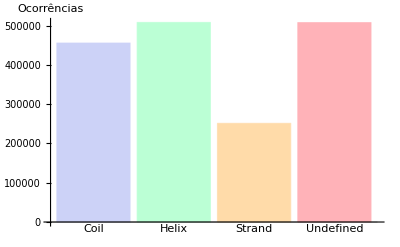

```mathematica
barSS = BarChart[{{ssOCC[[1]], ssOCC[[4]], ssOCC[[3]], ssOCC[[2]]}}, PlotTheme->"Classic", ChartLabels->{"Coil", "Helix", "Strand", "Undefined"}, AxesLabel->{None, "Ocorrências"}]
```

```mathematica
Export["~/Documentos/PhD-Quali/latex/quali/figures/occ_ss.pdf", barSS]
```

~/Documentos/PhD-Quali/latex/quali/figures/occ_ss.pdf